## Tracking a ramp (Problem 9.11)

```mathematica
Clear["Global`*"];
```

```mathematica
g=1/(1+s)^2; q=((1+s)^2 (a+b s))/(1+s τ)^3; (* g is the system, q is the IMC controller *)
T=q g
```

(a+b s)/(1+s τ)^3

```mathematica
S=1-T//Together
```

(1-a-b s+3 s τ+3 s^2 τ^2+s^3 τ^3)/(1+s τ)^3

```mathematica
S0=S/.{a->1,b->3τ}
```

(3 s^2 τ^2+s^3 τ^3)/(1+s τ)^3

```mathematica
k=q/S0/.{a->1,b->3τ}
```

((1+s)^2 (1+3 s τ))/(3 s^2 τ^2+s^3 τ^3)

```mathematica
gtf=TransferFunctionModel[g,s];Ttf=TransferFunctionModel[T/.{a->1,b->3τ},s];
utf=TransferFunctionModel[k S0,s];
```

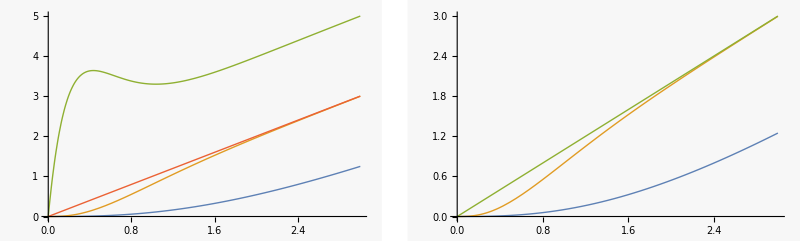

```mathematica
u=UnitStep[t];tmax=3;u=t;τ=1/3;
yout=OutputResponse[Ttf,u,{t,0,tmax}]; gout=OutputResponse[gtf,u,{t,0,tmax}];
uout=OutputResponse[utf,u,{t,0,tmax}];
p1=Plot[{gout,yout,uout,u},{t,0,tmax},PlotRange->All];
p2=Plot[{gout,yout,u},{t,0,tmax},PlotRange->All];
GraphicsRow[{p1,p2}]
```

```mathematica
kold=TransferFunctionModel[(1+s)^2/(τ s(2+τ s)),s]; (* for tracking step only *)
```

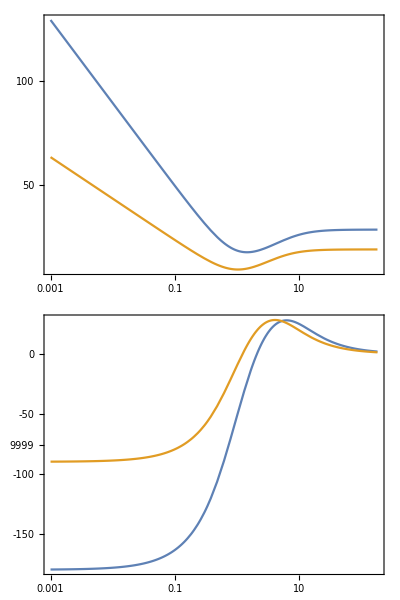

```mathematica
BodePlot[{k,kold}]  (* compare the controllers for tracking step & ramp *)
```

Export data.

```mathematica
dt=0.01;dat = Table[{ yout[[1]],uout[[1]],gout[[1]]},{t,0,tmax,dt}];
```

```mathematica
(*  
SetDirectory[NotebookDirectory[]];
Export["IMCramp1.dat", dat];
*)
```